## Tupik_D_L

## Lab_work_2: Символьные вычисления в системе Mathematica

## 2.1

### 1.

```mathematica
t1 = (6 * (x^3 + 27) * (x^4 - y^4))/((x^2 - 4) * (x^2 + y^2)) + 4 *(x+y)^2 + x^3 + y^3
```

x^3+y^3+4 (x+y)^2+(6 (27+x^3) (x^4-y^4))/((-4+x^2) (x^2+y^2))

```mathematica
Expand[t1]
```

4 x^2+x^3+8 x y+4 y^2+y^3+(162 x^4)/((-4+x^2) (x^2+y^2))+(6 x^7)/((-4+x^2) (x^2+y^2))-(162 y^4)/((-4+x^2) (x^2+y^2))-(6 x^3 y^4)/((-4+x^2) (x^2+y^2))

```mathematica
ExpandAll[t1]
```

4 x^2+x^3+8 x y+4 y^2+y^3+(162 x^4)/(-4 x^2+x^4-4 y^2+x^2 y^2)+(6 x^7)/(-4 x^2+x^4-4 y^2+x^2 y^2)-(162 y^4)/(-4 x^2+x^4-4 y^2+x^2 y^2)-(6 x^3 y^4)/(-4 x^2+x^4-4 y^2+x^2 y^2)

```mathematica
Factor[t1]
```

((x+y) (146 x-4 x^2+4 x^3+7 x^4-178 y+4 x y+4 x^2 y-7 x^3 y-4 y^2+x^2 y^2))/((-2+x) (2+x))

```mathematica
Together[t1]
```

(146 x^2-4 x^3+4 x^4+7 x^5-32 x y+8 x^3 y-178 y^2+4 x^2 y^2-6 x^3 y^2-4 y^3+x^2 y^3)/(-4+x^2)

```mathematica
Apart[t1]
```

(x^2 (146-4 x+4 x^2+7 x^3))/((-2+x) (2+x))+8 x y-(2 (89-2 x^2+3 x^3) y^2)/((-2+x) (2+x))+y^3

```mathematica
Cancel[t1]
```

x^3+y^3+4 (x+y)^2+(6 (27+x^3) (x^2-y^2))/(-4+x^2)

```mathematica
Simplify[t1]
```

x^3+y^3+4 (x+y)^2+(6 (27+x^3) (x^2-y^2))/(-4+x^2)

### 2.

```mathematica
t2 = Numerator[Together[t1]]
```

146 x^2-4 x^3+4 x^4+7 x^5-32 x y+8 x^3 y-178 y^2+4 x^2 y^2-6 x^3 y^2-4 y^3+x^2 y^3

```mathematica
Collect[t2, x]
```

4 x^4+7 x^5-32 x y-178 y^2-4 y^3+x^3 (-4+8 y-6 y^2)+x^2 (146+4 y^2+y^3)

```mathematica
Collect[t2, y]
```

146 x^2-4 x^3+4 x^4+7 x^5+(-32 x+8 x^3) y+(-178+4 x^2-6 x^3) y^2+(-4+x^2) y^3

```mathematica
Exponent[t2, x]
```

5

```mathematica
Exponent[t2, y]
```

3

```mathematica
Coefficient[t2, x, 5]
```

7

```mathematica
Coefficient[t2, y, 1]
```

-32 x+8 x^3

## 2.2

### 1.

```mathematica
D[x^n * Cos[x], x]
```

n x^(-1+n) Cos[x]-x^n Sin[x]

### 2.

```mathematica
D[(a*x^3+2*x^2),x]
```

4 x+3 a x^2

```mathematica
D[4*x^2 - 5*x + 8 - 3/x, {x, 3}]
```

18/x^4

```mathematica
D[x^3*y^2 + 3 * x^2, {x, 3}, {y,2}]
```

12

### 3.

```mathematica
Integrate[1/(x^2 - 1), x]
```

1/2 Log[1-x]-1/2 Log[1+x]

### 4.

```mathematica
Integrate[x^3/(x^2 + 1), x]
```

x^2/2-1/2 Log[1+x^2]

```mathematica
Together[D[x^2/2-1/2 Log[1+x^2], x] ]
```

x^3/(1+x^2)

```mathematica
Integrate[1/(x^3 + 1), x]
```

ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2]

```mathematica
ExpandAll[Together[D[ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2], x]]]
```

1/(1+x^3)

### 5.

```mathematica
Integrate[5*x - 2 * Sqrt[x] + 32/x^3, {x, 1, 4}]
```

259/6

### 6.

```mathematica
Integrate[(1+x^4)^(1/3), {x, 0, 1}]
```

Hypergeometric2F1[-1/3,1/4,5/4,-1]

```mathematica
Integrate[(1+x^4)^(1/3), {x, 0, 1.}]
```

1.05753

## 1.3

### 1.

```mathematica
Solve[a * x^4 + x^2 + 3 == 0, x]
```

{{x→-(√(-1/a-(√(1-12 a))/a))/(√2)},{x→(√(-1/a-(√(1-12 a))/a))/(√2)},{x→-(√(-1/a+(√(1-12 a))/a))/(√2)},{x→(√(-1/a+(√(1-12 a))/a))/(√2)}}

### 2.

```mathematica
Solve[x^2 + y == 1 && y^2 - x^2 == 2, {x, y}]
```

{{x→-ⅈ √(1/2 (-3+√13)),y→1/2 (-1+√13)},{x→ⅈ √(1/2 (-3+√13)),y→1/2 (-1+√13)},{x→-√(1/2 (3+√13)),y→1/2 (-1-√13)},{x→√(1/2 (3+√13)),y→1/2 (-1-√13)}}

### 3.

```mathematica
solve = NSolve[x^2 - y^2 == 1 && y^3 + x== 5, {x, y}]
```

{{x→-0.928941-1.39823 ⅈ,y→-0.788459-1.64735 ⅈ},{x→-0.928941+1.39823 ⅈ,y→-0.788459+1.64735 ⅈ},{x→1.78303,y→1.47621},{x→-2.17236,y→1.9285},{x→1.1236-1.05808 ⅈ,y→-0.913899+1.30087 ⅈ},{x→1.1236+1.05808 ⅈ,y→-0.913899-1.30087 ⅈ}}

```mathematica
Length [solve]
```

6

### 4.

```mathematica
DSolve[y'[x]-y[x]*Tan[x]==x,y[x],x]
```

{{y[x]→C[1] Sec[x]+Sec[x] (Cos[x]+x Sin[x])}}

```mathematica
line41 = DSolveValue[{y'[x]-y[x]*Tan[x]==x,y'[1] == 1 },y[x],x]
```

1-Cos[1] Sec[x]-Sec[x] Sin[1]+x Tan[x]

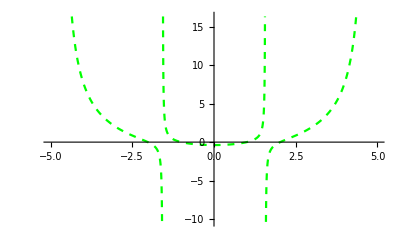

```mathematica
Show[Plot[line41, {x, -5, 5},PlotStyle->{Dashed, Green}]]
```

```mathematica
DSolve[y'[x]+y[x]Tan[x]== 1/Cos[x], y[x],x]
```

{{y[x]→C[1] Cos[x]+Sin[x]}}

```mathematica
line42 = DSolveValue[{y'[x]+y[x]Tan[x]== 1/Cos[x], y'[1] == 1}, y[x],x]
```

Cos[x] Cot[1]-Cos[x] Csc[1]+Sin[x]

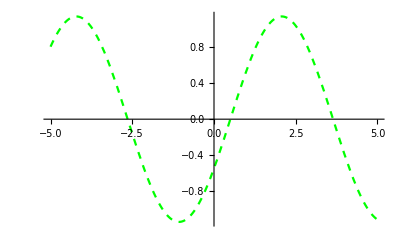

```mathematica
Show[Plot[line42, {x, -5, 5},PlotStyle->{Dashed, Green}]]
```

### 5.

```mathematica
DSolve[y''[x]-y'[x]+x*y[x]==0,y[x],x]
```

{{y[x]→ⅇ^(x/2) AiryAi[-(-1)^(1/3) (1/4-x)] C[1]+ⅇ^(x/2) AiryBi[-(-1)^(1/3) (1/4-x)] C[2]}}

```mathematica
t51= FullSimplify[DSolve[{y''[x]-y'[x]+x*y[x]==0, y[0]==2, y'[0]==1}, y[x], x]]
```

{{y[x]→-2 ⅇ^(x/2) π (AiryAiPrime[1/4] AiryBi[1/4-x]-AiryAi[1/4-x] AiryBiPrime[1/4])}}

```mathematica
t52 = NDSolve[{y''[x]-y'[x]+x*y[x]==0, y[0]==2, y'[0]==1}, y[x], {x, -10,10}]
```

{{y[x]→InterpolatingFunction[…][x]}}

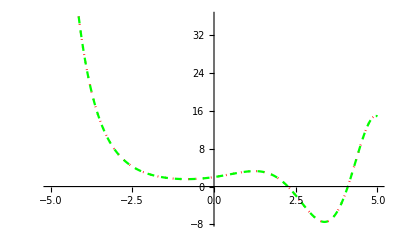

```mathematica
line1:= Plot[t51[[1,1,2]],{x,-5,5},PlotStyle->{Dotted, Red}]
line2 := Plot[t52[[1, 1, 2]], {x, -5, 5},PlotStyle->{Dashed, Green}]
t53 = Show[line1, line2]
```